# Harmonic Oscillator

## Classical Oscillator

Plot classical trajectories for a particle subject to a parabolic V(x), e.g., a ball rolling on a parabolic surface with no friction.

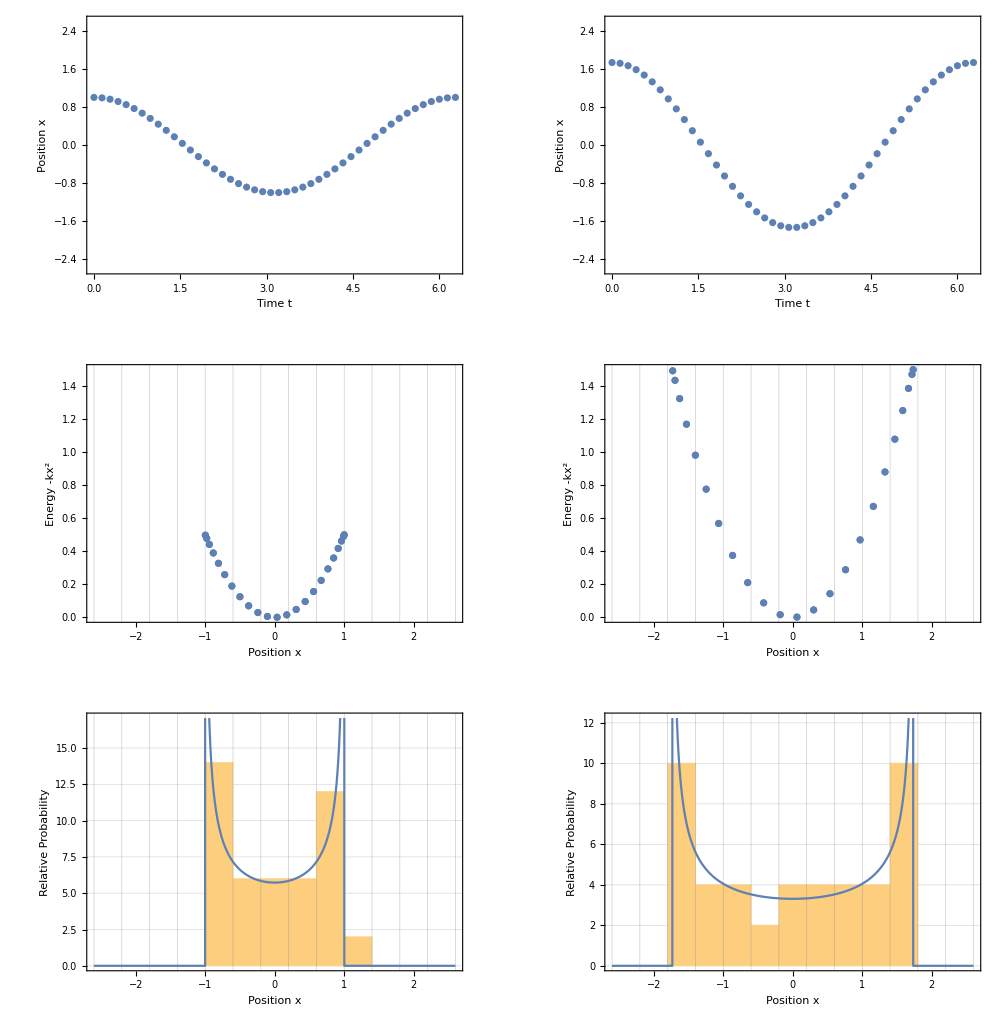

```mathematica
With[{ω=1,m=1,EA=1/2,EB=3/2,nt=45,nx=13,xlim=2.6},
Module[{T,k,xA,xB,tvec,dx,pdfA,pdfB,xvec,xvecA,xvecB,yvecA,yvecB,opt1,opt2,opt3},
T=2π/ω;
k=m ω^2;
xA=Sqrt[2 EA/k];
xB=Sqrt[2 EB/k];
tvec=Range[0,T,T/nt];
dx=2xlim/nx;
pdfA=Function[x,If[x^2<xA^2,2nt dx/(2π Sqrt[xA^2-x^2]),0]];
pdfB=Function[x,If[x^2<xB^2,2nt dx/(2π Sqrt[xB^2-x^2]),0]];
xvec=Range[-xlim,+xlim,dx];
xvecA=xA Cos[ω tvec];
xvecB=xB Cos[ω tvec];
yvecA=k xvecA^2/2;
yvecB=k xvecB^2/2;
opt1={PlotRange->{{0,T},{-xlim,+xlim}},PlotStyle->Thin,PlotRangePadding->Scaled[0.02],Frame->True,GridLines->{tvec,xvec},FrameLabel->{"Time t","Position x"}};
opt2={PlotRange->{{-xlim,+xlim},{0,EB}},PlotStyle->Thin,PlotRangePadding->Scaled[0.02],Frame->True,GridLines->{xvec,None},FrameLabel->{"Position x","Energy -kx^2"}};
opt3={Frame->True,FrameLabel->{"Position x","Relative Probability"},Axes->None,GridLines->{xvec,Automatic}};
GraphicsGrid[{
{
ListPlot[Transpose[{tvec,xvecA}],opt1],
ListPlot[Transpose[{tvec,xvecB}],opt1],
},
{
ListPlot[Transpose[{xvecA,yvecA}],opt2],
ListPlot[Transpose[{xvecB,yvecB}],opt2]
},
{
Show[{
Histogram[xvecA,{xvec},opt3],
Plot[pdfA[x],{x,-xlim,+xlim}]
}],
Show[{
Histogram[xvecB,{xvec},opt3],
Plot[pdfB[x],{x,-xlim,+xlim}]
}]
}
},ImageSize->1000]
]
]
```

```mathematica
parabola[nmax_:0]:=
Show[{
Plot[x^2,{x,-2.6,+2.6},GridLines->{Range[-2.6,2.6,0.2],Range[0,7.5,0.5]},Frame->True,FrameLabel->{"Position x (arb.units)","Height y(x) (arb.units)"}],
ListPlot[Table[{Sqrt[2n+1],(2n+1)},{n,0,nmax}],PlotStyle->Directive[Red,PointSize[0.03]]]
}]
```

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Activities/parabola.pdf",parabola[0]]
```

/Users/david/Documents/uci/Teaching/113A/Activities/parabola.pdf

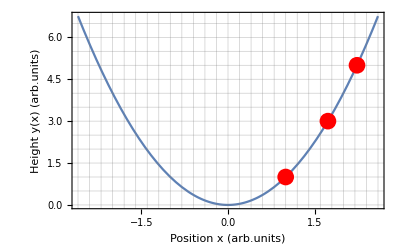

```mathematica
parabola[2]
```

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Activities/spacetime.pdf",
ListPlot[{},PlotRange->{{0,1},{-2.6,+2.6}},Frame->True,FrameLabel->{"Time t/T","Position x (arb.units)"},GridLines->{Range[0,1,1/45],Range[-2.6,2.6,0.4]},GridLinesStyle->{LightGray,Directive[Gray,Dashed]}]
]
```

/Users/david/Documents/uci/Teaching/113A/Activities/spacetime.pdf

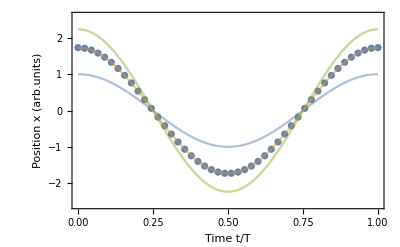

```mathematica
Show[{
ListPlot[Table[{t,Sqrt[3]Cos[2π t]},{t,0,1,1/45}],PlotRange->{{0,1},{-2.6,+2.6}},Frame->True,FrameLabel->{"Time t/T","Position x (arb.units)"},GridLines->{Range[0,1,1/45],Range[-2.6,2.6,0.4]},GridLinesStyle->{LightGray,Directive[Gray,Dashed]}],
Plot[{Cos[2π t],Sqrt[3]Cos[2π t],Sqrt[5]Cos[2π t]},{t,0,1},PlotStyle->Opacity[0.5]]
}]
```

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Activities/histogram.pdf",
ListPlot[{},PlotRange->{{-2.6,+2.6},{0,11}},Frame->True,FrameLabel->{"Position x (arb.units)","Number of Dots"},GridLines->{Range[-2.6,2.6,0.4],Range[10]},GridLinesStyle->{Directive[Gray,Dashed],LightGray},FrameTicks->{Automatic,Range[10]}]
]
```

/Users/david/Documents/uci/Teaching/113A/Activities/histogram.pdf

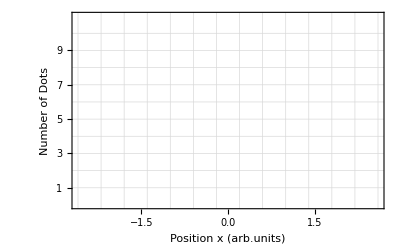

```mathematica
ListPlot[{},PlotRange->{{-2.6,+2.6},{0,11}},Frame->True,FrameLabel->{"Position x (arb.units)","Number of Dots"},GridLines->{Range[-2.6,2.6,0.4],Range[10]},GridLinesStyle->{Directive[Gray,Dashed],LightGray},FrameTicks->{Automatic,Range[10]}]
```

## Classical Limit

Define the PDF for finding a classical oscillator at x given its amplitude x0:

```mathematica
pdf[x_,x0_]:=1/(π √(-x^2+x0^2))UnitStep[x+x0]UnitStep[x0-x]
```

Compare with the corresponding quantum stationary states, using the normalized position s = (mω/ℏ)^(1/2)x:

```mathematica
ψ[n_]:=Function[s,π^(-1/4)HermiteH[n,s]Exp[-s^2/2]/Sqrt[2^n n!]]
```

Calculate the classical turning point where V(s) = E for the n-th state:

```mathematica
smax[n_]:=Sqrt[2n+1]
```

Compare the classical and quantum PDFs for a specified state:

```mathematica
Clear[plotHO]
plotHO[n_,OptionsPattern[]]:=
With[{
slim=OptionValue["slim"],
npt=OptionValue["npt"]
},
Module[{x0,svec,pdfC,pdfQ,ymax},
svec=Range[-slim,+slim,2 slim/npt];
pdfC=Table[pdf[s,smax[n]],{s,svec}];
pdfQ=Table[ψ[n][s]^2,{s,svec}];
ymax=Max[pdfQ];
(* offset points slightly to better show regions where the value is zero *)
pdfC += 0.002 ymax;
pdfQ += 0.002 ymax;
ListPlot[{Transpose[{svec,pdfQ}],Transpose[{svec,pdfC}]},PlotStyle->{Thickness[0.002],Directive[Red,Thickness[0.001]]},Joined->True,
Filling->{1->0,2->{0,Directive[Red,Opacity[0.1]]}},Frame->True,ImageMargins->{{0,4},{0,4}},Axes->None,FrameLabel->{"Position x/(mω/ℏ)^(1/2)","Probability Density"},PlotRange->{{-slim,+slim},{0,1.05 ymax}},FrameTicks->{Automatic,None},LabelStyle->Large,ImageSize->{1024,768},AspectRatio->Full,Epilog->{Text[Style["n="<>ToString[n],FontSize->40,FontFamily->"Times",FontSlant->"Italic"],Scaled[{0.02,0.95}],{-1,0}]}
]
]
]
Options[plotHO]={"slim"->11,"npt"->2001};
```

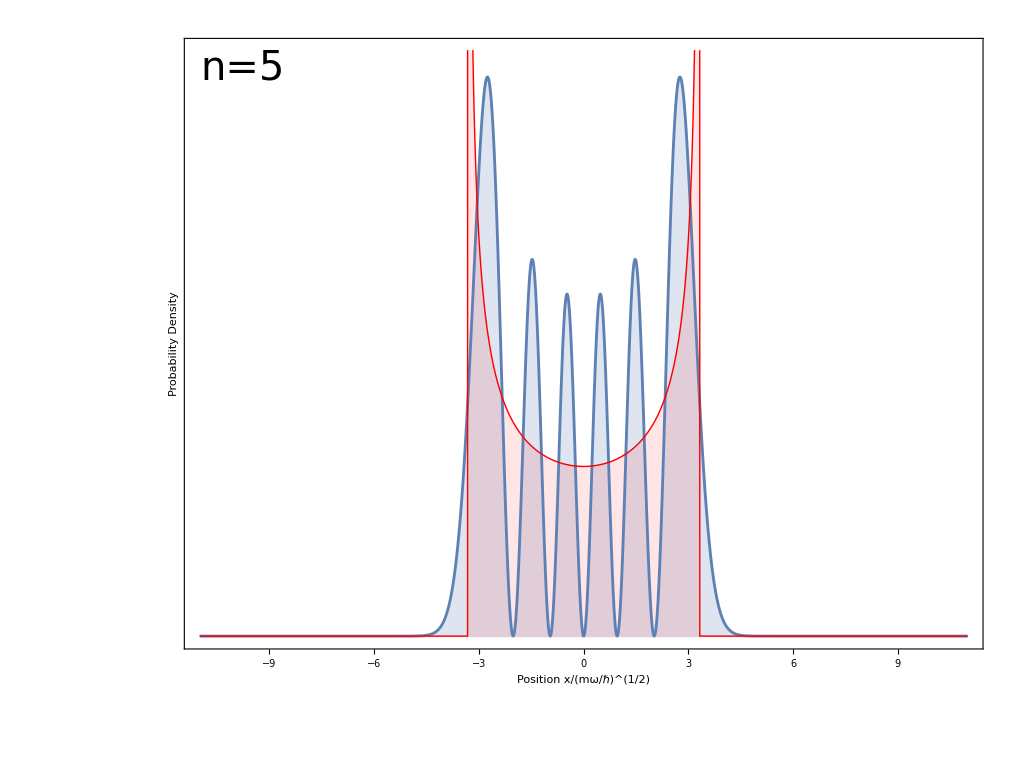

```mathematica
plotHO[5]
```

Generate frames for n = 0-50:

```mathematica
Timing[frames=Table[plotHO[n],{n,0,50}];]
```

{25.4953,Null}

Animate frames so that the amplitude increases linearly and more time is spent displaying smaller values of n.  Pause on the last frame.

```mathematica
durations=N[Table[Sqrt[150/(2n+1)]/8,{n,0,49}]];
durations=Append[durations,2 durations[[1]]]
```

{1.53093,0.883883,0.684653,0.578638,0.51031,0.461593,0.424604,0.395285,0.371305,0.35122,0.334077,0.319221,0.306186,0.294628,0.284287,0.274963,0.266501,0.258775,0.251684,0.245145,0.239091,0.233465,0.228218,0.223309,0.218704,0.214373,0.21029,0.206431,0.202777,0.19931,0.196016,0.192879,0.189889,0.187033,0.184302,0.181688,0.179182,0.176777,0.174466,0.172243,0.170103,0.168042,0.166053,0.164133,0.162278,0.160485,0.15875,0.15707,0.155443,0.153864,3.06186}

```mathematica
Export["/Users/david/Desktop/harmonic.gif",frames,AnimationRepetitions->Infinity,"DisplayDurations"->durations]
```

/Users/david/Desktop/harmonic.gif